8/1/2021  AMJ version

4/25/2021  Now I have combined the vector and the density plots.  ATM I am liking pastelColors for the density, and black vectors scaled “Log” and there is a very visible difference between the vectors on the surface of the sphere towards the wire and the surface away from the wire.

4/17/2021  This is just for plotting the momentum density around the charged sphere, near two current carrying wires, both z-directed, one at x=+dWire/2, the other at -dWire/2, both at y = 0.

```mathematica
ClearAll["Global`*"]
```

```mathematica
mu0 = 4 * Pi * 10^-7;
eps0 = 8.854188 10^-12;
speedOfLight = 2.99792 10^8;
JoulesToEV = 6.2415093433 * 10^18;
a = 5.0 10^-4 ;

(* information for the two wires  *)
current = 1.0;
rWire =  a ;
dWire = 20. a;     (*  Distance between the two wires  *)
x0Wire =dWire/2.0 ;       y0Wire = 0.;     z0Wire = 0.;
rhoL0 = 10^-15;

(* information for the charged sphere  *)
qSphere = 1.0 10^-15;
rSphere = a ;
x0Sphere = x0Wire + 3. rSphere  ;      y0Sphere = 0.;  z0Sphere = 0.;  (*  distance from origen to center of the sphere  *)

(* The following are for the ListVectorPlot table  *)
xRange = 4.  rSphere ;    X0 = x0Wire + rWire;
xColumns =16;
DeltaX = xRange/(xColumns-1);

zRange = xRange;    Z0 = -zRange/2.;
zRows = xColumns;
DeltaZ = zRange/(zRows-1);
```

First find hField due to the wire.  The magnitude of H a distance r from the wire is just I/(2 Pi r).  Considering the center of the wire as the origin, and the direction of H is in the plus θ .

```mathematica
phi[x_, y_]:= ArcTan[x, y] + Pi/2.;
hFieldX1[x_, y_]:= If[    Sqrt[(x-dWire/2.)^2+ y^2] < rWire, 0.,       current/(2 Pi Sqrt[(x-dWire/2.)^2+ y^2])   Cos[phi[(x-dWire/2.), y] ]  ];
hFieldX2[x_, y_]:= If[    Sqrt[(x+dWire/2.)^2+ y^2] < rWire, 0.,-current/(2 Pi Sqrt[(x+dWire/2.)^2+ y^2])   Cos[phi[(x+dWire/2.), y] ]  ];
hFieldY1[x_, y_]:= If[    Sqrt[(x-dWire/2.)^2+ y^2] < rWire, 0.,   current/(2 Pi Sqrt[(x-dWire/2.)^2+ y^2])   Sin[phi[(x-dWire/2.), y] ] ];
hFieldY2[x_, y_]:= If[    Sqrt[(x+dWire/2.)^2+ y^2] < rWire, 0.,   -current/(2 Pi Sqrt[(x+dWire/2.)^2+ y^2])  Sin[phi[(x+dWire/2.), y] ] ];
hField[x_, y_, z_] := {hFieldX1[x, y]+ hFieldX2[x, y], hFieldY1[x, y] + hFieldY2[x, y], 0.};
```

Now for the eField.  This will be due to a hollow sphere of charge q1 located at  {x0Sphere,  0.,  0.}
Reusing my code from the two charged spheres notebook.

```mathematica
eFieldCart[x_, y_, z_] := 
If [Sqrt[(x-x0Sphere)^2 +y^2+ z^2] < rSphere, 0., 1.]  qSphere/(4 π eps0( (x-x0Sphere)^2+y^2+ z^2)){ (x-x0Sphere)/Sqrt[(x-x0Sphere)^2  + y^2 + z^2], y/Sqrt[(x-x0Sphere)^2  + y^2 + z^2], z/Sqrt[(x-x0Sphere)^2  + y^2 + z^2]}
```

Since the wire is in the z direction, we only have Hx and Hy

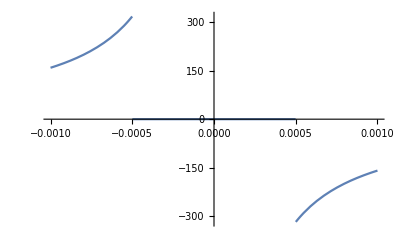

```mathematica
Plot[hFieldX1[dWire/2., y], {y, -2. a, 2. a}, PlotRange->All]
```

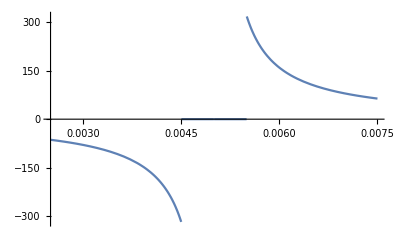

```mathematica
Plot[hFieldY1[x, 0], {x,5. a, 15. a}, PlotRange->All]
```

This is just for plotting, now, the actual integration over space is in other tables

```mathematica
XNow = X0;
ZNow = Z0;
listNum = 0;
oneList = Table[{{0, 0}, {0, 0}}, {i, 1, xColumns*zRows}];
```

```mathematica
For[i=1, i<xColumns+1,i++, 
For[j=1, j<zRows+1,j++, 
listNum++;
oneList[[listNum]][[1]][[1]] = ZNow;
oneList[[listNum]][[1]][[2]] = XNow;
oneList[[listNum]][[2]][[1]] =  Cross[eFieldCart[XNow, 0., ZNow], hField[XNow, 0., ZNow]][[3]];
oneList[[listNum]][[2]][[2]] = Cross[eFieldCart[XNow, 0., ZNow], hField[XNow, 0., ZNow]][[1]];
ZNow  = Z0 + DeltaZ (j);
];
XNow  = X0 + DeltaX (i);
ZNow = Z0;
]
```

```mathematica
legendsa=StringForm["|``|   kg/(s m^2)", Style[g,Bold]]
legendsb = "|g|   kg/(s m^2)"
```

|g|   kg/(s m^2)

|g|   kg/(s m^2)

```mathematica
legends=StringForm["|``|   kg/(s m^2)", Style[g,Bold]];ECrossH[x_, z_] := Cross[eFieldCart[x,0., z], hField[x, 0., z]]
pVector[x_, z_] :={   {ECrossH[x, z][[3]]}, { ECrossH[x, z][[1]]}    } / (speedOfLight * speedOfLight);
pVector1[x_, z_] :=If[z<X0, {0., 0.}, pVector[x, z]]
Plot11 = DensityPlot[Norm[pVector[x,z]], {z, Z0 , Z0 + zRange}, {x, X0, X0 +xRange}, ColorFunction->"Rainbow", PlotPoints -> 50 ,  FrameLabel -> {"z (mm)", "x (mm)"},LabelStyle->Directive[Black, FontSize -> 16],FrameTicks->  {    {{#,1000 #}&/@FindDivisions[{X0, X0 +xRange},5] //N,Automatic},{{#,1000#}&/@FindDivisions[{Z0 , Z0 + zRange},5] //N,Automatic}   } ,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->legendsb],{After,Center}] ]
```

-Graphics-

```mathematica
X0-rWire/2. -X0 +xRange

Z0 -rWire/4. - Z0 + zRange+rWire/4.
```

0.00175

0.002

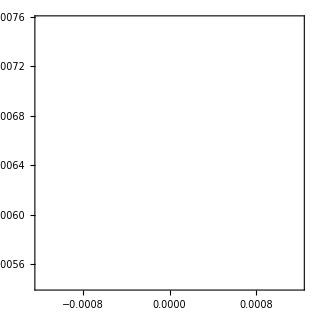

```mathematica
Plot12 = VectorPlot[pVector[x,z], {z, Z0 -rWire/4., Z0 + zRange+rWire/4.}, {x, X0, X0 +xRange}, VectorScaling -> "Linear", VectorColorFunction->None, VectorStyle->{White, Thickness[0.003]} ]
```

```mathematica
Show [Plot11, Plot12]
```

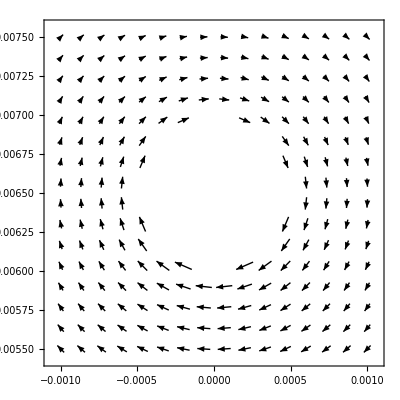

```mathematica
PlotBlack = ListVectorPlot[oneList, DataRange->{ {Z0, Z0 + DeltaZ*(zRows-1)}, {X0, X0 + DeltaX*(xColumns-1)} }, VectorPoints->All, VectorScaling -> Sqrt, VectorColorFunction->None, VectorStyle->Black]
```

```mathematica
qEnclosed[r_]:= If[r < rSphere, (qSphere r^3)/a^3, qSphere];
eField[r_] := qEnclosed[r]/(4 π r^2 eps0);
potSphereTEMP[r_] = -Integrate[eField[r], r ]
potInfinity = Limit[potSphereTEMP[r], {r -> ∞} ]
potSphere[r_] := potSphereTEMP[r] - potInfinity 

potSphereCartesian[x_, y_, z_] := potSphere[√((x-x0Sphere)^2+(y-y0Sphere)^2+(z-z0Sphere)^2)]
```

-(Piecewise[{{35950.2 r^2, r≤0.0005}, {0.0269627-(8.98755×10^-6)/r, True}}])

-0.0269627

```mathematica
Plot1 = DensityPlot[ potSphereCartesian[x, 0., z]*1000.,  {z,- 2 rSphere, 2rSphere }, {x, x0Sphere - 2rSphere, x0Sphere + 2 rSphere },PlotRange->All, Exclusions->None, ColorFunction->"Pastel",
 FrameLabel -> {"z (mm)", "x (mm)"},
Frame -> True, PlotLabel -> "ϕ(z,x) and momentum density",FrameTicks->  {    {{#,1000 #}&/@FindDivisions[{0.0055, 0.0075},5] //N,Automatic},{{#,1000#}&/@FindDivisions[{-0.001, 0.001},7] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->"ϕ(z,x) in mV"],{After,Center}] ]
```

-Graphics-

```mathematica
Show[ Plot1, PlotBlack,PlotRange->All]
```

-Graphics-

```mathematica
Onelist
```

Onelist